# 25. Ways to apply Function

```mathematica
f[x]
```

f[x]

```mathematica
f@x
```

f[x]

```mathematica
x//f
```

f[x]

```mathematica
2 π^3+1 // N
```

63.0126

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
f[{1,2,3}]
```

f[{1,2,3}]

```mathematica
SetAttributes[f,Listable]
```

```mathematica
f[{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
Framed[x]
```

x

```mathematica
Hue/@Table[x,{x,0,1,0.1}]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9],Hue[1.]}

# 26. Pure anonymous functions

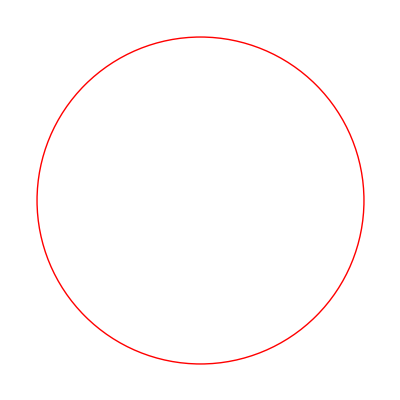
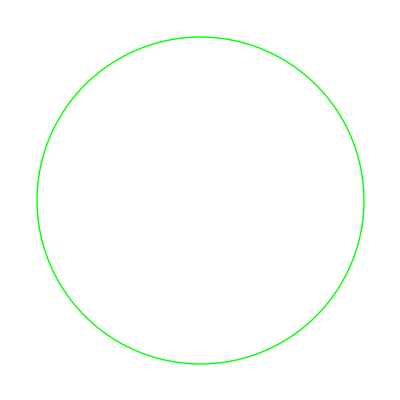
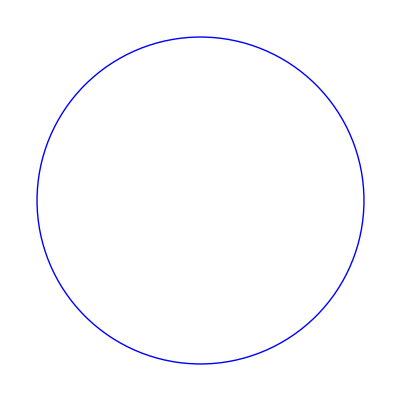

```mathematica
Graphics/@{Style[Circle[],Red],Style[Circle[],Green],Style[Circle[],Blue]}
```

```mathematica
Blur /@%
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Blur[#,5]&/@%
```

```mathematica
Rotate[#,90Degree]&/@{"one","two","three"}
```

{one,two,three}

```mathematica
Graphics[Circle[], ImageSize->#]&/@{10,20,30,20,10}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Framed[Column[{#,ColorNegate[#]}]]& /@ {Cyan,Magenta,Yellow,Black}
```

{RGBColor[0, 1, 1]
RGBColor[1., 0., 0.],RGBColor[1, 0, 1]
RGBColor[0., 1., 0.],RGBColor[1, 1, 0]
RGBColor[0., 0., 1.],GrayLevel[0]
GrayLevel[1.]}

```mathematica
{#,StringLength[WikipediaData[#]]}&/@{"9/11","Columbine"}
```

```mathematica
{{"9/11",89355},{"Columbine",2348}}//Grid
```

9/11 | 89355
Columbine | 2348

```mathematica
Style[#,Hue[#/10],5#]&/@IntegerDigits[2^100]
```

{1,2,6,7,6,5,0,6,0,0,2,2,8,2,2,9,4,0,1,4,9,6,7,0,3,2,0,5,3,7,6}

```mathematica
g[#,{x,#},{#,#}]&/@{a,b,c}
```

```mathematica
{g[a,{x,a},{a,a}],g[b,{x,b},{b,b}],g[c,{x,c},{c,c}]}//Column
```

g[a,{x,a},{a,a}]
g[b,{x,b},{b,b}]
g[c,{x,c},{c,c}]

```mathematica
f[#,a]&@{x,y,z}
```

{f[x,a],f[y,a],f[z,a]}

```mathematica
Column[{#,ColorNegate[#],#}]&[Blend[{Red,Yellow}]]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

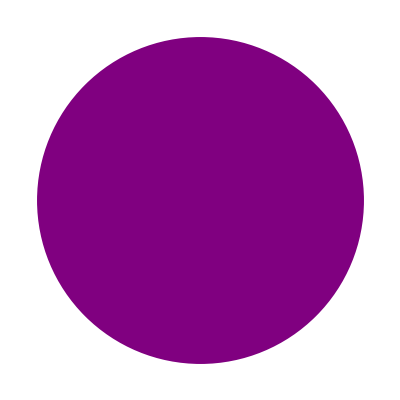

```mathematica
Style[Disk[],Purple]//Graphics
```

```mathematica
NestList[EdgeDetect,%,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

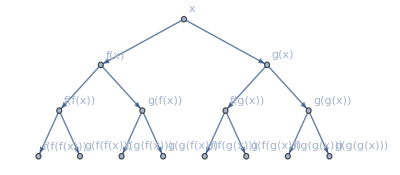

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->All]
```